# Mu3e sensitivity to parameter space

Find our list of signal and background events, along with associated parameters

```mathematica
sigdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events","*"}];
bkgdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-background","Events","*"}];
sigfiles=FileNames[FileNameJoin[{sigdirs,"unweighted_events.lhe.gz"}]];
bkgfile=FileNames[FileNameJoin[{bkgdirs,"unweighted_events.lhe.gz"}]];
paramfiles=FileNames[FileNameJoin[{sigdirs,"report.dat"}]];
files=Transpose[{sigfiles,paramfiles}];
nRuns=files//Length;
nb=FileNameJoin[{NotebookDirectory[],"analyze-run.nb"}];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"madevent-analysis.nb"}]]
```

Call our analysis notebook on each set and let us know if it is sensitive or not

```mathematica
paramspace=Reap[
Do[
sig=files[[i,1]];
bkg=bkgfile[[1]];
params=Import[files[[i,2]]];
mphi=params[[3,2]];
gsm=params[[4,2]];
gse=params[[5,2]];
pattern="m_ϕ=``, g_ϕμ=``, g_ϕe=``:";
sensitive=NotebookEvaluate[nb];
Sow[{mphi,gsm,gse,sensitive}];
If[sensitive,Print[StringForm[pattern<>" sensitive",mphi,gsm,gse]];
,Print[StringForm[pattern<>" NOT sensitive",mphi,gsm,gse]]],
{i,nRuns}]][[2]][[1]]
```

m_ϕ=0.0015, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0015, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0015, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.00668421, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.00668421, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0118684, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0118684, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0170526, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0170526, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0222368, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0222368, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0274211, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0274211, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0326053, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0326053, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0377895, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0377895, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0429737, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0429737, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0481579, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0481579, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0533421, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0533421, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0585263, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0585263, g_ϕμ=0.001, g_ϕe=1.×10^-6: sensitive

m_ϕ=0.0637105, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0637105, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0688947, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.074079, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0792632, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0844474, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0896316, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.0948158, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=1.×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=1.43845×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=2.06914×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=2.97635×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=4.28133×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=6.15848×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=8.85867×10^-6, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000127428, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000183298, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000263665, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.0000379269, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000054556, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000078476, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000112884, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000162378, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000233572, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000335982, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000483293, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.000695193, g_ϕe=1.×10^-6: NOT sensitive

m_ϕ=0.1, g_ϕμ=0.001, g_ϕe=1.×10^-6: NOT sensitive

{{0.0015,1.×10^-6,1.×10^-6,False},{0.0015,1.43845×10^-6,1.×10^-6,False},{0.0015,2.06914×10^-6,1.×10^-6,False},{0.0015,2.97635×10^-6,1.×10^-6,False},{0.0015,4.28133×10^-6,1.×10^-6,False},{0.0015,6.15848×10^-6,1.×10^-6,False},{0.0015,8.85867×10^-6,1.×10^-6,False},{0.0015,0.0000127428,1.×10^-6,False},{0.0015,0.0000183298,1.×10^-6,False},{0.0015,0.0000263665,1.×10^-6,True},{0.0015,0.0000379269,1.×10^-6,True},{0.0015,0.000054556,1.×10^-6,True},{0.0015,0.000078476,1.×10^-6,True},{0.0015,0.000112884,1.×10^-6,True},{0.0015,0.000162378,1.×10^-6,True},{0.0015,0.000233572,1.×10^-6,True},{0.0015,0.000335982,1.×10^-6,True},{0.0015,0.000483293,1.×10^-6,True},{0.0015,0.000695193,1.×10^-6,True},{0.0015,0.001,1.×10^-6,True},{0.00668421,1.×10^-6,1.×10^-6,False},{0.00668421,1.43845×10^-6,1.×10^-6,False},{0.00668421,2.06914×10^-6,1.×10^-6,False},{0.00668421,2.97635×10^-6,1.×10^-6,False},{0.00668421,4.28133×10^-6,1.×10^-6,False},{0.00668421,6.15848×10^-6,1.×10^-6,False},{0.00668421,8.85867×10^-6,1.×10^-6,False},{0.00668421,0.0000127428,1.×10^-6,False},{0.00668421,0.0000183298,1.×10^-6,False},{0.00668421,0.0000263665,1.×10^-6,False},{0.00668421,0.0000379269,1.×10^-6,True},{0.00668421,0.000054556,1.×10^-6,True},{0.00668421,0.000078476,1.×10^-6,True},{0.00668421,0.000112884,1.×10^-6,True},{0.00668421,0.000162378,1.×10^-6,True},{0.00668421,0.000233572,1.×10^-6,True},{0.00668421,0.000335982,1.×10^-6,True},{0.00668421,0.000483293,1.×10^-6,True},{0.00668421,0.000695193,1.×10^-6,True},{0.00668421,0.001,1.×10^-6,True},{0.0118684,1.×10^-6,1.×10^-6,False},{0.0118684,1.43845×10^-6,1.×10^-6,False},{0.0118684,2.06914×10^-6,1.×10^-6,False},{0.0118684,2.97635×10^-6,1.×10^-6,False},{0.0118684,4.28133×10^-6,1.×10^-6,False},{0.0118684,6.15848×10^-6,1.×10^-6,False},{0.0118684,8.85867×10^-6,1.×10^-6,False},{0.0118684,0.0000127428,1.×10^-6,False},{0.0118684,0.0000183298,1.×10^-6,False},{0.0118684,0.0000263665,1.×10^-6,False},{0.0118684,0.0000379269,1.×10^-6,False},{0.0118684,0.000054556,1.×10^-6,True},{0.0118684,0.000078476,1.×10^-6,True},{0.0118684,0.000112884,1.×10^-6,True},{0.0118684,0.000162378,1.×10^-6,True},{0.0118684,0.000233572,1.×10^-6,True},{0.0118684,0.000335982,1.×10^-6,True},{0.0118684,0.000483293,1.×10^-6,True},{0.0118684,0.000695193,1.×10^-6,True},{0.0118684,0.001,1.×10^-6,True},{0.0170526,1.×10^-6,1.×10^-6,False},{0.0170526,1.43845×10^-6,1.×10^-6,False},{0.0170526,2.06914×10^-6,1.×10^-6,False},{0.0170526,2.97635×10^-6,1.×10^-6,False},{0.0170526,4.28133×10^-6,1.×10^-6,False},{0.0170526,6.15848×10^-6,1.×10^-6,False},{0.0170526,8.85867×10^-6,1.×10^-6,False},{0.0170526,0.0000127428,1.×10^-6,False},{0.0170526,0.0000183298,1.×10^-6,False},{0.0170526,0.0000263665,1.×10^-6,False},{0.0170526,0.0000379269,1.×10^-6,False},{0.0170526,0.000054556,1.×10^-6,True},{0.0170526,0.000078476,1.×10^-6,True},{0.0170526,0.000112884,1.×10^-6,True},{0.0170526,0.000162378,1.×10^-6,True},{0.0170526,0.000233572,1.×10^-6,True},{0.0170526,0.000335982,1.×10^-6,True},{0.0170526,0.000483293,1.×10^-6,True},{0.0170526,0.000695193,1.×10^-6,True},{0.0170526,0.001,1.×10^-6,True},{0.0222368,1.×10^-6,1.×10^-6,False},{0.0222368,1.43845×10^-6,1.×10^-6,False},{0.0222368,2.06914×10^-6,1.×10^-6,False},{0.0222368,2.97635×10^-6,1.×10^-6,False},{0.0222368,4.28133×10^-6,1.×10^-6,False},{0.0222368,6.15848×10^-6,1.×10^-6,False},{0.0222368,8.85867×10^-6,1.×10^-6,False},{0.0222368,0.0000127428,1.×10^-6,False},{0.0222368,0.0000183298,1.×10^-6,False},{0.0222368,0.0000263665,1.×10^-6,False},{0.0222368,0.0000379269,1.×10^-6,False},{0.0222368,0.000054556,1.×10^-6,False},{0.0222368,0.000078476,1.×10^-6,True},{0.0222368,0.000112884,1.×10^-6,True},{0.0222368,0.000162378,1.×10^-6,True},{0.0222368,0.000233572,1.×10^-6,True},{0.0222368,0.000335982,1.×10^-6,True},{0.0222368,0.000483293,1.×10^-6,True},{0.0222368,0.000695193,1.×10^-6,True},{0.0222368,0.001,1.×10^-6,True},{0.0274211,1.×10^-6,1.×10^-6,False},{0.0274211,1.43845×10^-6,1.×10^-6,False},{0.0274211,2.06914×10^-6,1.×10^-6,False},{0.0274211,2.97635×10^-6,1.×10^-6,False},{0.0274211,4.28133×10^-6,1.×10^-6,False},{0.0274211,6.15848×10^-6,1.×10^-6,False},{0.0274211,8.85867×10^-6,1.×10^-6,False},{0.0274211,0.0000127428,1.×10^-6,False},{0.0274211,0.0000183298,1.×10^-6,False},{0.0274211,0.0000263665,1.×10^-6,False},{0.0274211,0.0000379269,1.×10^-6,False},{0.0274211,0.000054556,1.×10^-6,False},{0.0274211,0.000078476,1.×10^-6,False},{0.0274211,0.000112884,1.×10^-6,True},{0.0274211,0.000162378,1.×10^-6,True},{0.0274211,0.000233572,1.×10^-6,True},{0.0274211,0.000335982,1.×10^-6,True},{0.0274211,0.000483293,1.×10^-6,True},{0.0274211,0.000695193,1.×10^-6,True},{0.0274211,0.001,1.×10^-6,True},{0.0326053,1.×10^-6,1.×10^-6,False},{0.0326053,1.43845×10^-6,1.×10^-6,False},{0.0326053,2.06914×10^-6,1.×10^-6,False},{0.0326053,2.97635×10^-6,1.×10^-6,False},{0.0326053,4.28133×10^-6,1.×10^-6,False},{0.0326053,6.15848×10^-6,1.×10^-6,False},{0.0326053,8.85867×10^-6,1.×10^-6,False},{0.0326053,0.0000127428,1.×10^-6,False},{0.0326053,0.0000183298,1.×10^-6,False},{0.0326053,0.0000263665,1.×10^-6,False},{0.0326053,0.0000379269,1.×10^-6,False},{0.0326053,0.000054556,1.×10^-6,False},{0.0326053,0.000078476,1.×10^-6,False},{0.0326053,0.000112884,1.×10^-6,False},{0.0326053,0.000162378,1.×10^-6,True},{0.0326053,0.000233572,1.×10^-6,True},{0.0326053,0.000335982,1.×10^-6,True},{0.0326053,0.000483293,1.×10^-6,True},{0.0326053,0.000695193,1.×10^-6,True},{0.0326053,0.001,1.×10^-6,True},{0.0377895,1.×10^-6,1.×10^-6,False},{0.0377895,1.43845×10^-6,1.×10^-6,False},{0.0377895,2.06914×10^-6,1.×10^-6,False},{0.0377895,2.97635×10^-6,1.×10^-6,False},{0.0377895,4.28133×10^-6,1.×10^-6,False},{0.0377895,6.15848×10^-6,1.×10^-6,False},{0.0377895,8.85867×10^-6,1.×10^-6,False},{0.0377895,0.0000127428,1.×10^-6,False},{0.0377895,0.0000183298,1.×10^-6,False},{0.0377895,0.0000263665,1.×10^-6,False},{0.0377895,0.0000379269,1.×10^-6,False},{0.0377895,0.000054556,1.×10^-6,False},{0.0377895,0.000078476,1.×10^-6,False},{0.0377895,0.000112884,1.×10^-6,False},{0.0377895,0.000162378,1.×10^-6,True},{0.0377895,0.000233572,1.×10^-6,True},{0.0377895,0.000335982,1.×10^-6,True},{0.0377895,0.000483293,1.×10^-6,True},{0.0377895,0.000695193,1.×10^-6,True},{0.0377895,0.001,1.×10^-6,True},{0.0429737,1.×10^-6,1.×10^-6,False},{0.0429737,1.43845×10^-6,1.×10^-6,False},{0.0429737,2.06914×10^-6,1.×10^-6,False},{0.0429737,2.97635×10^-6,1.×10^-6,False},{0.0429737,4.28133×10^-6,1.×10^-6,False},{0.0429737,6.15848×10^-6,1.×10^-6,False},{0.0429737,8.85867×10^-6,1.×10^-6,False},{0.0429737,0.0000127428,1.×10^-6,False},{0.0429737,0.0000183298,1.×10^-6,False},{0.0429737,0.0000263665,1.×10^-6,False},{0.0429737,0.0000379269,1.×10^-6,False},{0.0429737,0.000054556,1.×10^-6,False},{0.0429737,0.000078476,1.×10^-6,False},{0.0429737,0.000112884,1.×10^-6,False},{0.0429737,0.000162378,1.×10^-6,False},{0.0429737,0.000233572,1.×10^-6,True},{0.0429737,0.000335982,1.×10^-6,True},{0.0429737,0.000483293,1.×10^-6,True},{0.0429737,0.000695193,1.×10^-6,True},{0.0429737,0.001,1.×10^-6,True},{0.0481579,1.×10^-6,1.×10^-6,False},{0.0481579,1.43845×10^-6,1.×10^-6,False},{0.0481579,2.06914×10^-6,1.×10^-6,False},{0.0481579,2.97635×10^-6,1.×10^-6,False},{0.0481579,4.28133×10^-6,1.×10^-6,False},{0.0481579,6.15848×10^-6,1.×10^-6,False},{0.0481579,8.85867×10^-6,1.×10^-6,False},{0.0481579,0.0000127428,1.×10^-6,False},{0.0481579,0.0000183298,1.×10^-6,False},{0.0481579,0.0000263665,1.×10^-6,False},{0.0481579,0.0000379269,1.×10^-6,False},{0.0481579,0.000054556,1.×10^-6,False},{0.0481579,0.000078476,1.×10^-6,False},{0.0481579,0.000112884,1.×10^-6,False},{0.0481579,0.000162378,1.×10^-6,False},{0.0481579,0.000233572,1.×10^-6,True},{0.0481579,0.000335982,1.×10^-6,True},{0.0481579,0.000483293,1.×10^-6,True},{0.0481579,0.000695193,1.×10^-6,True},{0.0481579,0.001,1.×10^-6,True},{0.0533421,1.×10^-6,1.×10^-6,False},{0.0533421,1.43845×10^-6,1.×10^-6,False},{0.0533421,2.06914×10^-6,1.×10^-6,False},{0.0533421,2.97635×10^-6,1.×10^-6,False},{0.0533421,4.28133×10^-6,1.×10^-6,False},{0.0533421,6.15848×10^-6,1.×10^-6,False},{0.0533421,8.85867×10^-6,1.×10^-6,False},{0.0533421,0.0000127428,1.×10^-6,False},{0.0533421,0.0000183298,1.×10^-6,False},{0.0533421,0.0000263665,1.×10^-6,False},{0.0533421,0.0000379269,1.×10^-6,False},{0.0533421,0.000054556,1.×10^-6,False},{0.0533421,0.000078476,1.×10^-6,False},{0.0533421,0.000112884,1.×10^-6,False},{0.0533421,0.000162378,1.×10^-6,False},{0.0533421,0.000233572,1.×10^-6,False},{0.0533421,0.000335982,1.×10^-6,False},{0.0533421,0.000483293,1.×10^-6,True},{0.0533421,0.000695193,1.×10^-6,True},{0.0533421,0.001,1.×10^-6,True},{0.0585263,1.×10^-6,1.×10^-6,False},{0.0585263,1.43845×10^-6,1.×10^-6,False},{0.0585263,2.06914×10^-6,1.×10^-6,False},{0.0585263,2.97635×10^-6,1.×10^-6,False},{0.0585263,4.28133×10^-6,1.×10^-6,False},{0.0585263,6.15848×10^-6,1.×10^-6,False},{0.0585263,8.85867×10^-6,1.×10^-6,False},{0.0585263,0.0000127428,1.×10^-6,False},{0.0585263,0.0000183298,1.×10^-6,False},{0.0585263,0.0000263665,1.×10^-6,False},{0.0585263,0.0000379269,1.×10^-6,False},{0.0585263,0.000054556,1.×10^-6,False},{0.0585263,0.000078476,1.×10^-6,False},{0.0585263,0.000112884,1.×10^-6,False},{0.0585263,0.000162378,1.×10^-6,False},{0.0585263,0.000233572,1.×10^-6,False},{0.0585263,0.000335982,1.×10^-6,False},{0.0585263,0.000483293,1.×10^-6,True},{0.0585263,0.000695193,1.×10^-6,True},{0.0585263,0.001,1.×10^-6,True},{0.0637105,1.×10^-6,1.×10^-6,False},{0.0637105,1.43845×10^-6,1.×10^-6,False},{0.0637105,2.06914×10^-6,1.×10^-6,False},{0.0637105,2.97635×10^-6,1.×10^-6,False},{0.0637105,4.28133×10^-6,1.×10^-6,False},{0.0637105,6.15848×10^-6,1.×10^-6,False},{0.0637105,8.85867×10^-6,1.×10^-6,False},{0.0637105,0.0000127428,1.×10^-6,False},{0.0637105,0.0000183298,1.×10^-6,False},{0.0637105,0.0000263665,1.×10^-6,False},{0.0637105,0.0000379269,1.×10^-6,False},{0.0637105,0.000054556,1.×10^-6,False},{0.0637105,0.000078476,1.×10^-6,False},{0.0637105,0.000112884,1.×10^-6,False},{0.0637105,0.000162378,1.×10^-6,False},{0.0637105,0.000233572,1.×10^-6,False},{0.0637105,0.000335982,1.×10^-6,False},{0.0637105,0.000483293,1.×10^-6,False},{0.0637105,0.000695193,1.×10^-6,False},{0.0637105,0.001,1.×10^-6,False},{0.0688947,1.×10^-6,1.×10^-6,False},{0.0688947,1.43845×10^-6,1.×10^-6,False},{0.0688947,2.06914×10^-6,1.×10^-6,False},{0.0688947,2.97635×10^-6,1.×10^-6,False},{0.0688947,4.28133×10^-6,1.×10^-6,False},{0.0688947,6.15848×10^-6,1.×10^-6,False},{0.0688947,8.85867×10^-6,1.×10^-6,False},{0.0688947,0.0000127428,1.×10^-6,False},{0.0688947,0.0000183298,1.×10^-6,False},{0.0688947,0.0000263665,1.×10^-6,False},{0.0688947,0.0000379269,1.×10^-6,False},{0.0688947,0.000054556,1.×10^-6,False},{0.0688947,0.000078476,1.×10^-6,False},{0.0688947,0.000112884,1.×10^-6,False},{0.0688947,0.000162378,1.×10^-6,False},{0.0688947,0.000233572,1.×10^-6,False},{0.0688947,0.000335982,1.×10^-6,False},{0.0688947,0.000483293,1.×10^-6,False},{0.0688947,0.000695193,1.×10^-6,False},{0.0688947,0.001,1.×10^-6,False},{0.074079,1.×10^-6,1.×10^-6,False},{0.074079,1.43845×10^-6,1.×10^-6,False},{0.074079,2.06914×10^-6,1.×10^-6,False},{0.074079,2.97635×10^-6,1.×10^-6,False},{0.074079,4.28133×10^-6,1.×10^-6,False},{0.074079,6.15848×10^-6,1.×10^-6,False},{0.074079,8.85867×10^-6,1.×10^-6,False},{0.074079,0.0000127428,1.×10^-6,False},{0.074079,0.0000183298,1.×10^-6,False},{0.074079,0.0000263665,1.×10^-6,False},{0.074079,0.0000379269,1.×10^-6,False},{0.074079,0.000054556,1.×10^-6,False},{0.074079,0.000078476,1.×10^-6,False},{0.074079,0.000112884,1.×10^-6,False},{0.074079,0.000162378,1.×10^-6,False},{0.074079,0.000233572,1.×10^-6,False},{0.074079,0.000335982,1.×10^-6,False},{0.074079,0.000483293,1.×10^-6,False},{0.074079,0.000695193,1.×10^-6,False},{0.074079,0.001,1.×10^-6,False},{0.0792632,1.×10^-6,1.×10^-6,False},{0.0792632,1.43845×10^-6,1.×10^-6,False},{0.0792632,2.06914×10^-6,1.×10^-6,False},{0.0792632,2.97635×10^-6,1.×10^-6,False},{0.0792632,4.28133×10^-6,1.×10^-6,False},{0.0792632,6.15848×10^-6,1.×10^-6,False},{0.0792632,8.85867×10^-6,1.×10^-6,False},{0.0792632,0.0000127428,1.×10^-6,False},{0.0792632,0.0000183298,1.×10^-6,False},{0.0792632,0.0000263665,1.×10^-6,False},{0.0792632,0.0000379269,1.×10^-6,False},{0.0792632,0.000054556,1.×10^-6,False},{0.0792632,0.000078476,1.×10^-6,False},{0.0792632,0.000112884,1.×10^-6,False},{0.0792632,0.000162378,1.×10^-6,False},{0.0792632,0.000233572,1.×10^-6,False},{0.0792632,0.000335982,1.×10^-6,False},{0.0792632,0.000483293,1.×10^-6,False},{0.0792632,0.000695193,1.×10^-6,False},{0.0792632,0.001,1.×10^-6,False},{0.0844474,1.×10^-6,1.×10^-6,False},{0.0844474,1.43845×10^-6,1.×10^-6,False},{0.0844474,2.06914×10^-6,1.×10^-6,False},{0.0844474,2.97635×10^-6,1.×10^-6,False},{0.0844474,4.28133×10^-6,1.×10^-6,False},{0.0844474,6.15848×10^-6,1.×10^-6,False},{0.0844474,8.85867×10^-6,1.×10^-6,False},{0.0844474,0.0000127428,1.×10^-6,False},{0.0844474,0.0000183298,1.×10^-6,False},{0.0844474,0.0000263665,1.×10^-6,False},{0.0844474,0.0000379269,1.×10^-6,False},{0.0844474,0.000054556,1.×10^-6,False},{0.0844474,0.000078476,1.×10^-6,False},{0.0844474,0.000112884,1.×10^-6,False},{0.0844474,0.000162378,1.×10^-6,False},{0.0844474,0.000233572,1.×10^-6,False},{0.0844474,0.000335982,1.×10^-6,False},{0.0844474,0.000483293,1.×10^-6,False},{0.0844474,0.000695193,1.×10^-6,False},{0.0844474,0.001,1.×10^-6,False},{0.0896316,1.×10^-6,1.×10^-6,False},{0.0896316,1.43845×10^-6,1.×10^-6,False},{0.0896316,2.06914×10^-6,1.×10^-6,False},{0.0896316,2.97635×10^-6,1.×10^-6,False},{0.0896316,4.28133×10^-6,1.×10^-6,False},{0.0896316,6.15848×10^-6,1.×10^-6,False},{0.0896316,8.85867×10^-6,1.×10^-6,False},{0.0896316,0.0000127428,1.×10^-6,False},{0.0896316,0.0000183298,1.×10^-6,False},{0.0896316,0.0000263665,1.×10^-6,False},{0.0896316,0.0000379269,1.×10^-6,False},{0.0896316,0.000054556,1.×10^-6,False},{0.0896316,0.000078476,1.×10^-6,False},{0.0896316,0.000112884,1.×10^-6,False},{0.0896316,0.000162378,1.×10^-6,False},{0.0896316,0.000233572,1.×10^-6,False},{0.0896316,0.000335982,1.×10^-6,False},{0.0896316,0.000483293,1.×10^-6,False},{0.0896316,0.000695193,1.×10^-6,False},{0.0896316,0.001,1.×10^-6,False},{0.0948158,1.×10^-6,1.×10^-6,False},{0.0948158,1.43845×10^-6,1.×10^-6,False},{0.0948158,2.06914×10^-6,1.×10^-6,False},{0.0948158,2.97635×10^-6,1.×10^-6,False},{0.0948158,4.28133×10^-6,1.×10^-6,False},{0.0948158,6.15848×10^-6,1.×10^-6,False},{0.0948158,8.85867×10^-6,1.×10^-6,False},{0.0948158,0.0000127428,1.×10^-6,False},{0.0948158,0.0000183298,1.×10^-6,False},{0.0948158,0.0000263665,1.×10^-6,False},{0.0948158,0.0000379269,1.×10^-6,False},{0.0948158,0.000054556,1.×10^-6,False},{0.0948158,0.000078476,1.×10^-6,False},{0.0948158,0.000112884,1.×10^-6,False},{0.0948158,0.000162378,1.×10^-6,False},{0.0948158,0.000233572,1.×10^-6,False},{0.0948158,0.000335982,1.×10^-6,False},{0.0948158,0.000483293,1.×10^-6,False},{0.0948158,0.000695193,1.×10^-6,False},{0.0948158,0.001,1.×10^-6,False},{0.1,1.×10^-6,1.×10^-6,False},{0.1,1.43845×10^-6,1.×10^-6,False},{0.1,2.06914×10^-6,1.×10^-6,False},{0.1,2.97635×10^-6,1.×10^-6,False},{0.1,4.28133×10^-6,1.×10^-6,False},{0.1,6.15848×10^-6,1.×10^-6,False},{0.1,8.85867×10^-6,1.×10^-6,False},{0.1,0.0000127428,1.×10^-6,False},{0.1,0.0000183298,1.×10^-6,False},{0.1,0.0000263665,1.×10^-6,False},{0.1,0.0000379269,1.×10^-6,False},{0.1,0.000054556,1.×10^-6,False},{0.1,0.000078476,1.×10^-6,False},{0.1,0.000112884,1.×10^-6,False},{0.1,0.000162378,1.×10^-6,False},{0.1,0.000233572,1.×10^-6,False},{0.1,0.000335982,1.×10^-6,False},{0.1,0.000483293,1.×10^-6,False},{0.1,0.000695193,1.×10^-6,False},{0.1,0.001,1.×10^-6,False}}

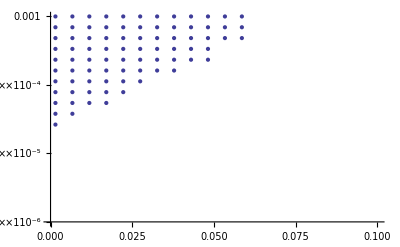

```mathematica
validparams=If[#1[[4]],{#1[[1]],#1[[2]]},##&[]]&/@paramspace;
ListLogPlot[validparams,PlotRange->{{0,0.1},{1*^-6,1*^-3}}]
```

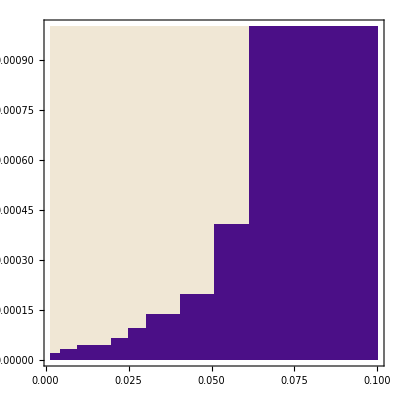

```mathematica
pl=Normal@ListContourPlot[If[#[[4]],{#[[1]],#[[2]],1},{#[[1]],#[[2]],0}]&/@paramspace,Contours->1,InterpolationOrder->0]
(*ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]*)
```